```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210210_impacts_in_time_windows"];
```

```mathematica
data=Import["data_with_time_windows.csv",HeaderLines->1];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
rawaim=data[[All,113]];
aim=DeleteCases[rawaim,"NA"];
campaign=Delete[data[[All,118]],Position[rawaim,"NA"]];
productionorder=Delete[data[[All,4]],Position[rawaim,"NA"]];
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["amount of production order ID's: ",Dimensions@DeleteDuplicates@productionorder]
Print["amount of customer ID's: ",Dimensions@DeleteDuplicates@Delete[data[[All,6]],Position[rawaim,"NA"]]]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {906}

aim data length: {32098}

amount of production order ID's: {5873}

amount of customer ID's: {399}

sequence data groups amount: {738}

```mathematica
range=Range[1200,1500];
check=Table[Mod[32098,i],{i,range}]
min=Min[check]
pos=Position[Table[Mod[32098,i],{i,range}],min(*Min[Table[Mod[32098,i],{i,Range[500,600]}]]*)][[1]]
bucketsize=range[[pos]]
```

{898,872,846,820,794,768,742,716,690,664,638,612,586,560,534,508,482,456,430,404,378,352,326,300,274,248,222,196,170,144,118,92,66,40,14,1223,1198,1173,1148,1123,1098,1073,1048,1023,998,973,948,923,898,873,848,823,798,773,748,723,698,673,648,623,598,573,548,523,498,473,448,423,398,373,348,323,298,273,248,223,198,173,148,123,98,73,48,23,1282,1258,1234,1210,1186,1162,1138,1114,1090,1066,1042,1018,994,970,946,922,898,874,850,826,802,778,754,730,706,682,658,634,610,586,562,538,514,490,466,442,418,394,370,346,322,298,274,250,226,202,178,154,130,106,82,58,34,10,1324,1301,1278,1255,1232,1209,1186,1163,1140,1117,1094,1071,1048,1025,1002,979,956,933,910,887,864,841,818,795,772,749,726,703,680,657,634,611,588,565,542,519,496,473,450,427,404,381,358,335,312,289,266,243,220,197,174,151,128,105,82,59,36,13,1386,1364,1342,1320,1298,1276,1254,1232,1210,1188,1166,1144,1122,1100,1078,1056,1034,1012,990,968,946,924,902,880,858,836,814,792,770,748,726,704,682,660,638,616,594,572,550,528,506,484,462,440,418,396,374,352,330,308,286,264,242,220,198,176,154,132,110,88,66,44,22,0,1438,1417,1396,1375,1354,1333,1312,1291,1270,1249,1228,1207,1186,1165,1144,1123,1102,1081,1060,1039,1018,997,976,955,934,913,892,871,850,829,808,787,766,745,724,703,682,661,640,619,598}

0

{260}

{1459}

```mathematica
bins=Table[MinMax[i],{i,Partition[Sort[aim],bucketsize]}]
(*bins=Sort@Join[Drop[bins,{3}],{{1220.10,1220.735},{1220.735,1221.37},{1221.37,1222.005},{1222.005,1222.64}}]*)
```

{{713.316,1103.64},{1103.64,1220.1},{1220.1,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1227.46},{1227.46,1231.58},{1231.58,1236.66},{1236.66,1255.08},{1255.08,1263.81},{1263.81,1277.3},{1277.3,1331.91},{1331.91,1372.04},{1372.66,1404.3},{1404.3,1449.39},{1449.39,1497.01},{1497.01,1507.05},{1507.05,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1534.85},{1534.85,2290.76}}

```mathematica
binning=Table[Catch[Do[If[IntervalMemberQ[Interval[i],aim[[j]]]==True,Throw[i]],
{i,bins}]],{j,Length[aim]}];
Position[binning,Null]
```

{}

```mathematica
aim=binning;
binningmembers=Sort[DeleteDuplicates[aim]]
Print["binning amount: ",Dimensions@DeleteDuplicates@binning]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

{{713.316,1103.64},{1103.64,1220.1},{1220.1,1222.64},{1222.64,1227.46},{1227.46,1231.58},{1231.58,1236.66},{1236.66,1255.08},{1255.08,1263.81},{1263.81,1277.3},{1277.3,1331.91},{1331.91,1372.04},{1372.66,1404.3},{1404.3,1449.39},{1449.39,1497.01},{1497.01,1507.05},{1507.05,1528.76},{1528.76,1534.85},{1534.85,2290.76}}

binning amount: {18,2}

dimension of binned data: {32098,2}

binning members dimension : {18,2}

```mathematica
(*part11=Take[Position[aim,{1220.10046386719,1222.64038085938}],1316];*)
part12=Take[Position[aim,{1220.10046386719,1222.64038085938}],{1317,2629}];
part13=Take[Position[aim,{1220.10046386719,1222.64038085938}],{2630,3942}];
part14=Take[Position[aim,{1220.10046386719,1222.64038085938}],-1313];
(*aim=ReplacePart[aim,part11->{"1220.1-1st","1222.64-1st"}];*)
aim=ReplacePart[aim,part12->{"1220.1-2nd","1222.64-2nd"}];
aim=ReplacePart[aim,part13->{"1220.1-3rd","1222.64-3rd"}];
aim=ReplacePart[aim,part14->{"1220.1-4th","1222.64-4th"}];

(*part21=Take[Position[aim,{1507.04553222656,1528.76245117188}],1256];*)
part22=Take[Position[aim,{1507.04553222656,1528.76245117188}],{1257,2510}];
part23=Take[Position[aim,{1507.04553222656,1528.76245117188}],{2511,3764}];
part24=Take[Position[aim,{1507.04553222656,1528.76245117188}],-1254];
(*aim=ReplacePart[aim,part21->{"1507.05-1st","1528.76-1st"}];*)
aim=ReplacePart[aim,part22->{"1507.05-2nd","1528.76-2nd"}];
aim=ReplacePart[aim,part23->{"1507.05-3rd","1528.76-3rd"}];
aim=ReplacePart[aim,part24->{"1507.05-4th","1528.76-4th"}];

(*{1449.38745117188,1497.01245117188}->2006,{1497.01245117188,1507.04553222656}->948*)
(*{1449.38745117188,1497.01245117188}->{1449.39,1450.02} 
{1497.01245117188,1507.04553222656}->{1450.02,1507.04}*)
part31=Take[Position[aim,{1449.38745117188,1497.01245117188}],-500];
part32=Position[aim,{1497.01245117188,1507.04553222656}];
part33=Take[Position[aim,{1449.38745117188,1497.01245117188}],1506];
aim=ReplacePart[aim,part31->{1450.02,1507.04}];
aim=ReplacePart[aim,part32->{1450.02,1507.04}];
aim=ReplacePart[aim,part33->{1449.39,1450.02}];
```

```mathematica
binningmembers=Sort[DeleteDuplicates[aim]]
```

{{713.316,1103.64},{1103.64,1220.1},{1220.1,1222.64},{1222.64,1227.46},{1227.46,1231.58},{1231.58,1236.66},{1236.66,1255.08},{1255.08,1263.81},{1263.81,1277.3},{1277.3,1331.91},{1331.91,1372.04},{1372.66,1404.3},{1404.3,1449.39},{1449.39,1450.02},{1450.02,1507.04},{1507.05,1528.76},{1528.76,1534.85},{1534.85,2290.76},{1220.1-2nd,1222.64-2nd},{1220.1-3rd,1222.64-3rd},{1220.1-4th,1222.64-4th},{1507.05-2nd,1528.76-2nd},{1507.05-3rd,1528.76-3rd},{1507.05-4th,1528.76-4th}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
productionorderbaskets=Values@GroupBy[Thread[{productionorder,aim}],Last->First];
productionorderbasketsrev=Table[DeleteDuplicates[i],{i,productionorderbaskets}];
Print["count of unique prod. order id's in each binning group: ",KeySort@Counts@Table[Length[i],{i,productionorderbasketsrev}]]
Print["binning groups association to count of unique prod. order id's: ",KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}]]
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

count of unique prod. order id's in each binning group: <|86→1,127→1,128→1,154→1,171→1,178→1,179→1,209→1,221→1,229→1,238→1,241→1,250→1,262→1,270→1,273→1,287→1,289→1,295→1,309→1,312→1,322→1,414→1,504→1|>

binning groups association to count of unique prod. order id's: <|{713.316,1103.64}→414,{1103.64,1220.1}→309,{1220.1,1222.64}→229,{1222.64,1227.46}→86,{1227.46,1231.58}→154,{1231.58,1236.66}→209,{1236.66,1255.08}→221,{1255.08,1263.81}→127,{1263.81,1277.3}→128,{1277.3,1331.91}→295,{1331.91,1372.04}→250,{1372.66,1404.3}→241,{1404.3,1449.39}→273,{1449.39,1450.02}→178,{1450.02,1507.04}→171,{1507.05,1528.76}→238,{1528.76,1534.85}→179,{1534.85,2290.76}→504,{1220.1-2nd,1222.64-2nd}→287,{1220.1-3rd,1222.64-3rd}→322,{1220.1-4th,1222.64-4th}→289,{1507.05-2nd,1528.76-2nd}→262,{1507.05-3rd,1528.76-3rd}→270,{1507.05-4th,1528.76-4th}→312|>

binning groups association to count of their total members: <|{713.316,1103.64}→1482,{1103.64,1220.1}→1439,{1220.1,1222.64}→1316,{1222.64,1227.46}→580,{1227.46,1231.58}→1753,{1231.58,1236.66}→1286,{1236.66,1255.08}→1352,{1255.08,1263.81}→1475,{1263.81,1277.3}→1455,{1277.3,1331.91}→1479,{1331.91,1372.04}→1411,{1372.66,1404.3}→1465,{1404.3,1449.39}→1472,{1449.39,1450.02}→1506,{1450.02,1507.04}→1448,{1507.05,1528.76}→1256,{1528.76,1534.85}→805,{1534.85,2290.76}→1417,{1220.1-2nd,1222.64-2nd}→1313,{1220.1-3rd,1222.64-3rd}→1313,{1220.1-4th,1222.64-4th}→1313,{1507.05-2nd,1528.76-2nd}→1254,{1507.05-3rd,1528.76-3rd}→1254,{1507.05-4th,1528.76-4th}→1254|>

binning amount: {24,2}

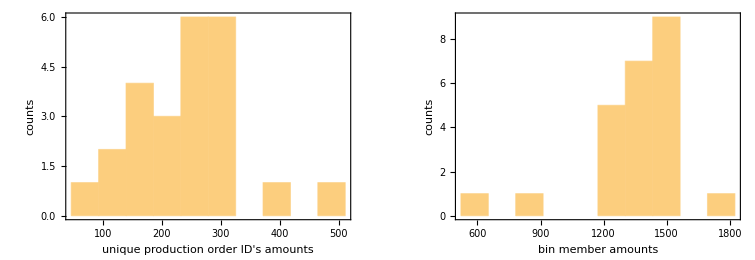

```mathematica
GraphicsRow[{Histogram[KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}],{"Raw",10},Frame->True,FrameLabel->{"unique production order ID's amounts","counts"},ImageSize->Full(*,PlotLabel->"Unique Production Order ID Counts for Each Bin"*)],Histogram[KeySort@Counts@aim,{"Raw",10},Frame->True,FrameLabel->{"bin member amounts","counts"},ImageSize->Full(*,PlotLabel->"Total Members Counts for Each Bin"*)]}]
```

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0283689,Null}

{24,2}

{276,2,2}

{738}

{1.7687,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0008115,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

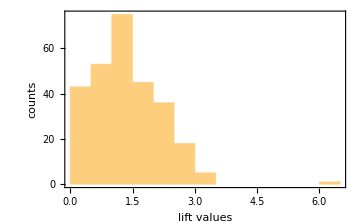

```mathematica
Histogram[liftvalues,PlotRange->All,Frame->True,FrameLabel->{"lift values","counts"},ImageSize->Medium]
```

{180,2,2}

{0.0233476,Null}

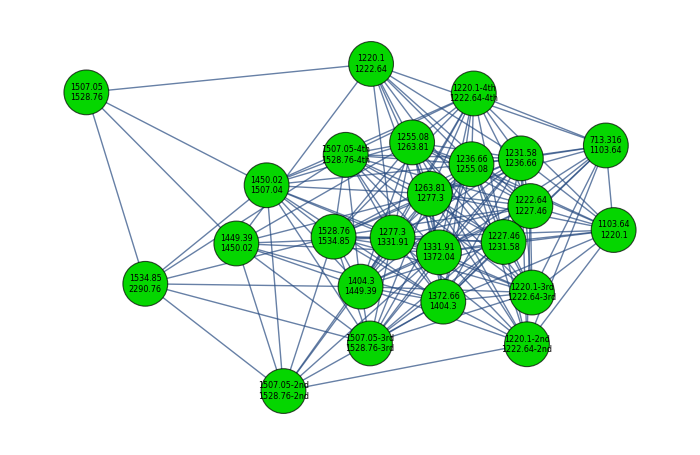

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1,VertexStyle->RGBColor[0.02,0.84,0.],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```